#### define variables

```mathematica
xc = 0;
yc = 0;
ptc = {xc,yc};
ptmax = {xmax, ymax};
npts = 10;
ri = 1;
kg = 2.1;
rg = ri *kg;
sunnyshady = Sin[0.3x]Sin[0.5y];
initialcircle = CirclePoints[ri, 10][[1]];
gradbound = Map[gradient, initialcircle]
```

{{0.3 Cos[0.3 x] Sin[0.5 y],0.5 Cos[0.5 y] Sin[0.3 x]}[1/4 (-1+√5)],{0.3 Cos[0.3 x] Sin[0.5 y],0.5 Cos[0.5 y] Sin[0.3 x]}[-√(5/8+(√5)/8)]}

#### define functions to use

```mathematica
findGradient[scalarFunc_,vars_]:=Grad[scalarFunc,vars]
```

```mathematica
gradthing[gradient_,xx_,yy_]:=gradient/.{x-> xx,y->yy}
```

#### find gradient

```mathematica
gradSunnyShady=findGradient[sunnyshady,{x,y}]
```

{0.3 Cos[0.3 x] Sin[0.5 y],0.5 Cos[0.5 y] Sin[0.3 x]}

```mathematica
gradthing[gradient,2,2]
```

{0.208349,0.152539}

#### draw things



```mathematica
p0 = Graphics[initialcircle]
```

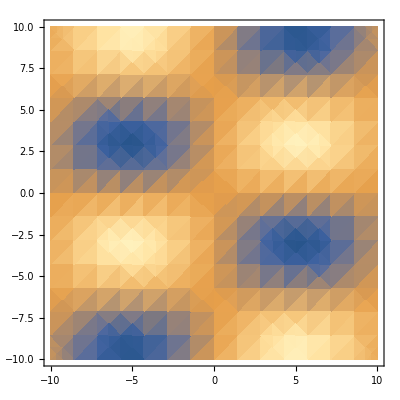

```mathematica
p1 = DensityPlot[Sin[0.3x]Sin[0.5y],{x,-10,10},{y,-10,10}]
```

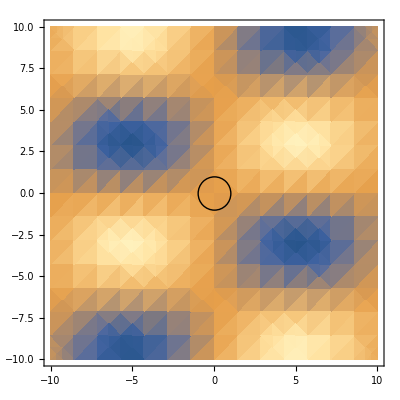

{}

```mathematica
Show[p1,p0]
```